```mathematica
Table[Labeled[Graph[EdgeList[allGraphs5[k,"graph"]],GraphLayout->"LayeredEmbedding", ImageSize->{50,50}, VertexLabels->"Name"]->allGraphs5[k,"graph"],k],{k,Sort[Bases["T","AtomKeys"]]}]
```

{-Graphics-→-Graphics-19936,-Graphics-→-Graphics-19940,-Graphics-→-Graphics-19969,-Graphics-→-Graphics-20029,-Graphics-→-Graphics-20060,-Graphics-→-Graphics-20721,-Graphics-→-Graphics-20812,-Graphics-→-Graphics-21420,-Graphics-→-Graphics-21510,-Graphics-→-Graphics-22287,-Graphics-→-Graphics-22318,-Graphics-→-Graphics-23072,-Graphics-→-Graphics-23770,-Graphics-→-Graphics-24384,-Graphics-→-Graphics-24414,-Graphics-→-Graphics-25168,-Graphics-→-Graphics-25868,-Graphics-→-Graphics-26821,-Graphics-→-Graphics-26852,-Graphics-→-Graphics-27610,-Graphics-→-Graphics-28308,-Graphics-→-Graphics-29128,-Graphics-→-Graphics-29888,-Graphics-→-Graphics-30586,-Graphics-→-Graphics-31224,-Graphics-→-Graphics-31984,-Graphics-→-Graphics-32684,-Graphics-→-Graphics-33130,-Graphics-→-Graphics-33158,-Graphics-→-Graphics-33916,-Graphics-→-Graphics-34620,-Graphics-→-Graphics-35434,-Graphics-→-Graphics-36194,-Graphics-→-Graphics-36898,-Graphics-→-Graphics-37548,-Graphics-→-Graphics-38308,-Graphics-→-Graphics-39014,-Graphics-→-Graphics-46180,-Graphics-→-Graphics-46184,-Graphics-→-Graphics-46942,-Graphics-→-Graphics-47694,-Graphics-→-Graphics-48460,-Graphics-→-Graphics-49220,-Graphics-→-Graphics-49972,-Graphics-→-Graphics-50718,-Graphics-→-Graphics-51478,-Graphics-→-Graphics-52232,-Graphics-→-Graphics-55252,-Graphics-→-Graphics-56012,-Graphics-→-Graphics-56770,-Graphics-→-Graphics-58288,-Graphics-→-Graphics-59048}

```mathematica
treeKeys=Bases["T","AtomKeys"]
```

{19936,46180,33130,24384,21420,26821,22287,20721,20029,19969,19940,55252,50718,47694,48460,46942,46184,37548,34620,35434,33916,33158,25868,31224,25168,24414,28308,23770,21510,29128,27610,26852,23072,22318,20812,20060,58288,56770,56012,52232,51478,49972,49220,39014,38308,36898,36194,32684,31984,30586,29888,59048}

```mathematica
Select[treeKeys,VertexCount[allGraphs5[#,"graph"]]==5&]
```

{19936}

```mathematica
Table[ShowGraph[allGraphs5,k]->GraphComplement[allGraphs5[k,"graph"]],{k,Select[Keys[allGraphs5],With[{g=allGraphs5[#,"graph"]},VertexCount[g]==5&&TreeGraphQ[g]]&]//Sort}]
```

{-Graphics-760→-Graphics-,-Graphics-766→-Graphics-,-Graphics-768→-Graphics-,-Graphics-814→-Graphics-,-Graphics-820→-Graphics-,-Graphics-822→-Graphics-,-Graphics-840→-Graphics-,-Graphics-846→-Graphics-,-Graphics-976→-Graphics-,-Graphics-982→-Graphics-,-Graphics-984→-Graphics-,-Graphics-1000→-Graphics-,-Graphics-1008→-Graphics-,-Graphics-1054→-Graphics-,-Graphics-1056→-Graphics-,-Graphics-1080→-Graphics-,-Graphics-2218→-Graphics-,-Graphics-2224→-Graphics-,-Graphics-2226→-Graphics-,-Graphics-2272→-Graphics-,-Graphics-2278→-Graphics-,-Graphics-2280→-Graphics-,-Graphics-2298→-Graphics-,-Graphics-2304→-Graphics-,-Graphics-2434→-Graphics-,-Graphics-2440→-Graphics-,-Graphics-2442→-Graphics-,-Graphics-2458→-Graphics-,-Graphics-2466→-Graphics-,-Graphics-2512→-Graphics-,-Graphics-2514→-Graphics-,-Graphics-2538→-Graphics-,-Graphics-2946→-Graphics-,-Graphics-2952→-Graphics-,-Graphics-3000→-Graphics-,-Graphics-3006→-Graphics-,-Graphics-3162→-Graphics-,-Graphics-3168→-Graphics-,-Graphics-3186→-Graphics-,-Graphics-3240→-Graphics-,-Graphics-6592→-Graphics-,-Graphics-6598→-Graphics-,-Graphics-6600→-Graphics-,-Graphics-6646→-Graphics-,-Graphics-6652→-Graphics-,-Graphics-6654→-Graphics-,-Graphics-6672→-Graphics-,-Graphics-6678→-Graphics-,-Graphics-6808→-Graphics-,-Graphics-6814→-Graphics-,-Graphics-6816→-Graphics-,-Graphics-6832→-Graphics-,-Graphics-6840→-Graphics-,-Graphics-6886→-Graphics-,-Graphics-6888→-Graphics-,-Graphics-6912→-Graphics-,-Graphics-7318→-Graphics-,-Graphics-7326→-Graphics-,-Graphics-7372→-Graphics-,-Graphics-7380→-Graphics-,-Graphics-7398→-Graphics-,-Graphics-7534→-Graphics-,-Graphics-7542→-Graphics-,-Graphics-7614→-Graphics-,-Graphics-8776→-Graphics-,-Graphics-8778→-Graphics-,-Graphics-8830→-Graphics-,-Graphics-8832→-Graphics-,-Graphics-8856→-Graphics-,-Graphics-8992→-Graphics-,-Graphics-8994→-Graphics-,-Graphics-9018→-Graphics-,-Graphics-9504→-Graphics-,-Graphics-9558→-Graphics-,-Graphics-9720→-Graphics-,-Graphics-19714→-Graphics-,-Graphics-19720→-Graphics-,-Graphics-19722→-Graphics-,-Graphics-19768→-Graphics-,-Graphics-19774→-Graphics-,-Graphics-19776→-Graphics-,-Graphics-19794→-Graphics-,-Graphics-19800→-Graphics-,-Graphics-19930→-Graphics-,-Graphics-19936→-Graphics-,-Graphics-19938→-Graphics-,-Graphics-19954→-Graphics-,-Graphics-19962→-Graphics-,-Graphics-20008→-Graphics-,-Graphics-20010→-Graphics-,-Graphics-20034→-Graphics-,-Graphics-20416→-Graphics-,-Graphics-20422→-Graphics-,-Graphics-20424→-Graphics-,-Graphics-20496→-Graphics-,-Graphics-20502→-Graphics-,-Graphics-20656→-Graphics-,-Graphics-20664→-Graphics-,-Graphics-20736→-Graphics-,-Graphics-21874→-Graphics-,-Graphics-21880→-Graphics-,-Graphics-21882→-Graphics-,-Graphics-21900→-Graphics-,-Graphics-21906→-Graphics-,-Graphics-22114→-Graphics-,-Graphics-22116→-Graphics-,-Graphics-22140→-Graphics-,-Graphics-22602→-Graphics-,-Graphics-22608→-Graphics-,-Graphics-22842→-Graphics-,-Graphics-26248→-Graphics-,-Graphics-26254→-Graphics-,-Graphics-26256→-Graphics-,-Graphics-26272→-Graphics-,-Graphics-26280→-Graphics-,-Graphics-26326→-Graphics-,-Graphics-26328→-Graphics-,-Graphics-26352→-Graphics-,-Graphics-26974→-Graphics-,-Graphics-26982→-Graphics-,-Graphics-27054→-Graphics-,-Graphics-28432→-Graphics-,-Graphics-28434→-Graphics-,-Graphics-28458→-Graphics-,-Graphics-29160→-Graphics-}

```mathematica
Table[ShowGraph[allGraphs5,k]->GraphComplement[allGraphs5[k,"graph"]],{k,Bases["G","AtomKeys"]//Sort}]
```

{-Graphics-0→-Graphics-,-Graphics-760→-Graphics-,-Graphics-2278→-Graphics-,-Graphics-3036→-Graphics-,-Graphics-3037→-Graphics-,-Graphics-6816→-Graphics-,-Graphics-7570→-Graphics-,-Graphics-7573→-Graphics-,-Graphics-9076→-Graphics-,-Graphics-9085→-Graphics-,-Graphics-9828→-Graphics-,-Graphics-9832→-Graphics-,-Graphics-9838→-Graphics-,-Graphics-9840→-Graphics-,-Graphics-9841→-Graphics-,-Graphics-20034→-Graphics-,-Graphics-20740→-Graphics-,-Graphics-20767→-Graphics-,-Graphics-22150→-Graphics-,-Graphics-22231→-Graphics-,-Graphics-22854→-Graphics-,-Graphics-22882→-Graphics-,-Graphics-22936→-Graphics-,-Graphics-22962→-Graphics-,-Graphics-22963→-Graphics-,-Graphics-26364→-Graphics-,-Graphics-26607→-Graphics-,-Graphics-27064→-Graphics-,-Graphics-27094→-Graphics-,-Graphics-27310→-Graphics-,-Graphics-27334→-Graphics-,-Graphics-27337→-Graphics-,-Graphics-28462→-Graphics-,-Graphics-28552→-Graphics-,-Graphics-28714→-Graphics-,-Graphics-28786→-Graphics-,-Graphics-28795→-Graphics-,-Graphics-29160→-Graphics-,-Graphics-29191→-Graphics-,-Graphics-29251→-Graphics-,-Graphics-29280→-Graphics-,-Graphics-29281→-Graphics-,-Graphics-29415→-Graphics-,-Graphics-29440→-Graphics-,-Graphics-29443→-Graphics-,-Graphics-29488→-Graphics-,-Graphics-29497→-Graphics-,-Graphics-29511→-Graphics-,-Graphics-29515→-Graphics-,-Graphics-29521→-Graphics-,-Graphics-29523→-Graphics-,-Graphics-29524→-Graphics-}

```mathematica
Forrest[-Graphics-]
```

False

```mathematica
KSetPartitions[Range[5],{5}]
```

KSetPartitions[{1,2,3,4,5},{5}]

```mathematica
SetPartitions[5]
```

{{{1,2,3,4,5}},{{1},{2,3,4,5}},{{1,2},{3,4,5}},{{1,3,4,5},{2}},{{1,2,3},{4,5}},{{1,4,5},{2,3}},{{1,2,4,5},{3}},{{1,3},{2,4,5}},{{1,2,3,4},{5}},{{1,5},{2,3,4}},{{1,2,5},{3,4}},{{1,3,4},{2,5}},{{1,2,3,5},{4}},{{1,4},{2,3,5}},{{1,2,4},{3,5}},{{1,3,5},{2,4}},{{1},{2},{3,4,5}},{{1},{2,3},{4,5}},{{1},{2,4,5},{3}},{{1},{2,3,4},{5}},{{1},{2,5},{3,4}},{{1},{2,3,5},{4}},{{1},{2,4},{3,5}},{{1,2},{3},{4,5}},{{1,3},{2},{4,5}},{{1,4,5},{2},{3}},{{1,2},{3,4},{5}},{{1,3,4},{2},{5}},{{1,5},{2},{3,4}},{{1,2},{3,5},{4}},{{1,3,5},{2},{4}},{{1,4},{2},{3,5}},{{1,2,3},{4},{5}},{{1,4},{2,3},{5}},{{1,5},{2,3},{4}},{{1,2,4},{3},{5}},{{1,3},{2,4},{5}},{{1,5},{2,4},{3}},{{1,2,5},{3},{4}},{{1,3},{2,5},{4}},{{1,4},{2,5},{3}},{{1},{2},{3},{4,5}},{{1},{2},{3,4},{5}},{{1},{2},{3,5},{4}},{{1},{2,3},{4},{5}},{{1},{2,4},{3},{5}},{{1},{2,5},{3},{4}},{{1,2},{3},{4},{5}},{{1,3},{2},{4},{5}},{{1,4},{2},{3},{5}},{{1,5},{2},{3},{4}},{{1},{2},{3},{4},{5}}}

```mathematica
PartitionToTreeGraph[part_List]:=Block[{nodes=Flatten[part],edges={}, head},
Table[
head=First[bucket];
Table[AppendTo[edges,UndirectedEdge[head,tail]],{tail,Rest[bucket]}]
,
{bucket,Select[part,Length[#]>1&]}];
Graph[nodes,edges, VertexLabels->"Name", ImageSize->{50,50}]
]
```

```mathematica
Tally[Map[PartitionToTreeGraph,SetPartitions[5]],IsomorphicGraphQ]
```

{{-Graphics-,1},{-Graphics-,5},{-Graphics-,10},{-Graphics-,10},{-Graphics-,15},{-Graphics-,10},{-Graphics-,1}}

```mathematica
PartitionToTreeGraphSignature[part_List]:=Block[{nodes=Sort[Flatten[part]],edges={}, head},
Table[
head=First[bucket];
Table[AppendTo[edges,UndirectedEdge[head,tail]],{tail,Rest[bucket]}]
,
{bucket,Select[part,Length[#]>1&]}];
GraphMatrixSignature[ AdjacencyMatrix[Graph[nodes,edges]]]
]
```

```mathematica
SetPartitions[5]
```

{{{1,2,3,4,5}},{{1},{2,3,4,5}},{{1,2},{3,4,5}},{{1,3,4,5},{2}},{{1,2,3},{4,5}},{{1,4,5},{2,3}},{{1,2,4,5},{3}},{{1,3},{2,4,5}},{{1,2,3,4},{5}},{{1,5},{2,3,4}},{{1,2,5},{3,4}},{{1,3,4},{2,5}},{{1,2,3,5},{4}},{{1,4},{2,3,5}},{{1,2,4},{3,5}},{{1,3,5},{2,4}},{{1},{2},{3,4,5}},{{1},{2,3},{4,5}},{{1},{2,4,5},{3}},{{1},{2,3,4},{5}},{{1},{2,5},{3,4}},{{1},{2,3,5},{4}},{{1},{2,4},{3,5}},{{1,2},{3},{4,5}},{{1,3},{2},{4,5}},{{1,4,5},{2},{3}},{{1,2},{3,4},{5}},{{1,3,4},{2},{5}},{{1,5},{2},{3,4}},{{1,2},{3,5},{4}},{{1,3,5},{2},{4}},{{1,4},{2},{3,5}},{{1,2,3},{4},{5}},{{1,4},{2,3},{5}},{{1,5},{2,3},{4}},{{1,2,4},{3},{5}},{{1,3},{2,4},{5}},{{1,5},{2,4},{3}},{{1,2,5},{3},{4}},{{1,3},{2,5},{4}},{{1,4},{2,5},{3}},{{1},{2},{3},{4,5}},{{1},{2},{3,4},{5}},{{1},{2},{3,5},{4}},{{1},{2,3},{4},{5}},{{1},{2,4},{3},{5}},{{1},{2,5},{3},{4}},{{1,2},{3},{4},{5}},{{1,3},{2},{4},{5}},{{1,4},{2},{3},{5}},{{1,5},{2},{3},{4}},{{1},{2},{3},{4},{5}}}

```mathematica
Map[PartitionToTreeGraphSignature,SetPartitions[5]]
```

{29160,351,19695,28431,26245,26245,28431,19695,28431,19695,26245,26245,28431,19695,26245,26245,12,244,324,324,244,324,244,19684,19684,26244,19692,26244,19684,19692,26244,19684,26244,19692,19692,26244,19692,19692,26244,19692,19692,1,9,9,243,243,243,19683,19683,19683,19683,0}

```mathematica
Table[ShowGraph[allGraphs5,k],{k,Sort[Map[PartitionToTreeGraphSignature,SetPartitions[5]]]}]
```

{-Graphics-0,-Graphics-1,-Graphics-3,-Graphics-9,-Graphics-12,-Graphics-27,-Graphics-36,-Graphics-81,-Graphics-84,-Graphics-108,-Graphics-243,-Graphics-244,-Graphics-270,-Graphics-324,-Graphics-351,-Graphics-729,-Graphics-738,-Graphics-810,-Graphics-972,-Graphics-1053,-Graphics-2187,-Graphics-2190,-Graphics-2214,-Graphics-2430,-Graphics-2457,-Graphics-2916,-Graphics-3159,-Graphics-6561,-Graphics-6562,-Graphics-6588,-Graphics-6642,-Graphics-6669,-Graphics-7290,-Graphics-7371,-Graphics-8748,-Graphics-8775,-Graphics-9477,-Graphics-19683,-Graphics-19684,-Graphics-19686,-Graphics-19692,-Graphics-19695,-Graphics-20412,-Graphics-20421,-Graphics-21870,-Graphics-21873,-Graphics-22599,-Graphics-26244,-Graphics-26245,-Graphics-26973,-Graphics-28431,-Graphics-29160}

```mathematica
vars=Table[PartitionToSymbol[part,"w"],{part,SetPartitions[5]}]
```

{w12345,w1x2345,w12x345,w1345x2,w123x45,w145x23,w1245x3,w13x245,w1234x5,w15x234,w125x34,w134x25,w1235x4,w14x235,w124x35,w135x24,w1x2x345,w1x23x45,w1x245x3,w1x234x5,w1x25x34,w1x235x4,w1x24x35,w12x3x45,w13x2x45,w145x2x3,w12x34x5,w134x2x5,w15x2x34,w12x35x4,w135x2x4,w14x2x35,w123x4x5,w14x23x5,w15x23x4,w124x3x5,w13x24x5,w15x24x3,w125x3x4,w13x25x4,w14x25x3,w1x2x3x45,w1x2x34x5,w1x2x35x4,w1x23x4x5,w1x24x3x5,w1x25x3x4,w12x3x4x5,w13x2x4x5,w14x2x3x5,w15x2x3x4,w1x2x3x4x5}

```mathematica
allGraphs5[0,"colofour"]
```

v12345+v1234x5+v1235x4+v123x45+v123x4x5+v1245x3+v124x35+v124x3x5+v125x34+v125x3x4+v12x345+v12x34x5+v12x35x4+v12x3x45+v12x3x4x5+v1345x2+v134x25+v134x2x5+v135x24+v135x2x4+v13x245+v13x24x5+v13x25x4+v13x2x45+v13x2x4x5+v145x23+v145x2x3+v14x235+v14x23x5+v14x25x3+v14x2x35+v14x2x3x5+v15x234+v15x23x4+v15x24x3+v15x2x34+v15x2x3x4+v1x2345+v1x234x5+v1x235x4+v1x23x45+v1x23x4x5+v1x245x3+v1x24x35+v1x24x3x5+v1x25x34+v1x25x3x4+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5

```mathematica
graphRep=Table[PartitionToSymbol[part,"w"]->ShowGraph[allGraphs5,PartitionToTreeGraphSignature[part]],{part,SetPartitions[5]}];
```

```mathematica
eqs=Table[PartitionToSymbol[part,"w"]==allGraphs5[PartitionToTreeGraphSignature[part],"colofour"],{part,SetPartitions[5]}]
```

{w12345==v1x2345+v1x234x5+v1x235x4+v1x23x45+v1x23x4x5+v1x245x3+v1x24x35+v1x24x3x5+v1x25x34+v1x25x3x4+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,w1x2345==v12x345+v12x34x5+v12x35x4+v12x3x45+v12x3x4x5+v1345x2+v134x2x5+v135x2x4+v13x2x45+v13x2x4x5+v145x2x3+v14x2x35+v14x2x3x5+v15x2x34+v15x2x3x4+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,w12x345==v13x245+v13x24x5+v13x25x4+v13x2x45+v13x2x4x5+v145x23+v145x2x3+v14x23x5+v14x25x3+v14x2x3x5+v15x23x4+v15x24x3+v15x2x3x4+v1x23x45+v1x23x4x5+v1x245x3+v1x24x3x5+v1x25x3x4+v1x2x3x45+v1x2x3x4x5,w1345x2==v12x345+v12x34x5+v12x35x4+v12x3x45+v12x3x4x5+v1x2345+v1x234x5+v1x235x4+v1x23x45+v1x23x4x5+v1x245x3+v1x24x35+v1x24x3x5+v1x25x34+v1x25x3x4+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,w123x45==v14x235+v14x23x5+v14x25x3+v14x2x35+v14x2x3x5+v15x234+v15x23x4+v15x24x3+v15x2x34+v15x2x3x4+v1x234x5+v1x235x4+v1x23x4x5+v1x24x35+v1x24x3x5+v1x25x34+v1x25x3x4+v1x2x34x5+v1x2x35x4+v1x2x3x4x5,w145x23==v12x345+v12x34x5+v12x35x4+v12x3x45+v12x3x4x5+v13x245+v13x24x5+v13x25x4+v13x2x45+v13x2x4x5+v1x245x3+v1x24x35+v1x24x3x5+v1x25x34+v1x25x3x4+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,w1245x3==v13x245+v13x24x5+v13x25x4+v13x2x45+v13x2x4x5+v1x2345+v1x234x5+v1x235x4+v1x23x45+v1x23x4x5+v1x245x3+v1x24x35+v1x24x3x5+v1x25x34+v1x25x3x4+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,w13x245==v12x345+v12x34x5+v12x35x4+v12x3x45+v12x3x4x5+v145x23+v145x2x3+v14x23x5+v14x2x35+v14x2x3x5+v15x23x4+v15x2x34+v15x2x3x4+v1x23x45+v1x23x4x5+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,w1234x5==v15x234+v15x23x4+v15x24x3+v15x2x34+v15x2x3x4+v1x2345+v1x234x5+v1x235x4+v1x23x45+v1x23x4x5+v1x245x3+v1x24x35+v1x24x3x5+v1x25x34+v1x25x3x4+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,w15x234==v12x345+v12x34x5+v12x35x4+v12x3x45+v12x3x4x5+v134x25+v134x2x5+v13x25x4+v13x2x45+v13x2x4x5+v14x25x3+v14x2x35+v14x2x3x5+v1x25x34+v1x25x3x4+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,w125x34==v13x245+v13x24x5+v13x25x4+v13x2x45+v13x2x4x5+v14x235+v14x23x5+v14x25x3+v14x2x35+v14x2x3x5+v1x235x4+v1x23x45+v1x23x4x5+v1x245x3+v1x24x35+v1x24x3x5+v1x25x3x4+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,w134x25==v12x345+v12x34x5+v12x35x4+v12x3x45+v12x3x4x5+v15x234+v15x23x4+v15x24x3+v15x2x34+v15x2x3x4+v1x234x5+v1x23x45+v1x23x4x5+v1x24x35+v1x24x3x5+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,w1235x4==v14x235+v14x23x5+v14x25x3+v14x2x35+v14x2x3x5+v1x2345+v1x234x5+v1x235x4+v1x23x45+v1x23x4x5+v1x245x3+v1x24x35+v1x24x3x5+v1x25x34+v1x25x3x4+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,w14x235==v12x345+v12x34x5+v12x35x4+v12x3x45+v12x3x4x5+v135x24+v135x2x4+v13x24x5+v13x2x45+v13x2x4x5+v15x24x3+v15x2x34+v15x2x3x4+v1x24x35+v1x24x3x5+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,w124x35==v13x245+v13x24x5+v13x25x4+v13x2x45+v13x2x4x5+v15x234+v15x23x4+v15x24x3+v15x2x34+v15x2x3x4+v1x234x5+v1x23x45+v1x23x4x5+v1x245x3+v1x24x3x5+v1x25x34+v1x25x3x4+v1x2x34x5+v1x2x3x45+v1x2x3x4x5,w135x24==v12x345+v12x34x5+v12x35x4+v12x3x45+v12x3x4x5+v14x235+v14x23x5+v14x25x3+v14x2x35+v14x2x3x5+v1x235x4+v1x23x45+v1x23x4x5+v1x25x34+v1x25x3x4+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,w1x2x345==v123x45+v123x4x5+v1245x3+v124x3x5+v125x3x4+v12x3x45+v12x3x4x5+v13x245+v13x24x5+v13x25x4+v13x2x45+v13x2x4x5+v145x23+v145x2x3+v14x23x5+v14x25x3+v14x2x3x5+v15x23x4+v15x24x3+v15x2x3x4+v1x23x45+v1x23x4x5+v1x245x3+v1x24x3x5+v1x25x3x4+v1x2x3x45+v1x2x3x4x5,w1x23x45==v124x35+v124x3x5+v125x34+v125x3x4+v12x34x5+v12x35x4+v12x3x4x5+v134x25+v134x2x5+v135x24+v135x2x4+v13x24x5+v13x25x4+v13x2x4x5+v14x25x3+v14x2x35+v14x2x3x5+v15x24x3+v15x2x34+v15x2x3x4+v1x24x35+v1x24x3x5+v1x25x34+v1x25x3x4+v1x2x34x5+v1x2x35x4+v1x2x3x4x5,w1x245x3==v123x45+v123x4x5+v12x345+v12x34x5+v12x35x4+v12x3x45+v12x3x4x5+v1345x2+v134x2x5+v135x2x4+v13x2x45+v13x2x4x5+v145x23+v145x2x3+v14x23x5+v14x2x35+v14x2x3x5+v15x23x4+v15x2x34+v15x2x3x4+v1x23x45+v1x23x4x5+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,w1x234x5==v125x34+v125x3x4+v12x345+v12x34x5+v12x35x4+v12x3x45+v12x3x4x5+v1345x2+v134x25+v134x2x5+v135x2x4+v13x25x4+v13x2x45+v13x2x4x5+v145x2x3+v14x25x3+v14x2x35+v14x2x3x5+v15x2x34+v15x2x3x4+v1x25x34+v1x25x3x4+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,w1x25x34==v123x45+v123x4x5+v124x35+v124x3x5+v12x35x4+v12x3x45+v12x3x4x5+v135x24+v135x2x4+v13x24x5+v13x2x45+v13x2x4x5+v145x23+v145x2x3+v14x23x5+v14x2x35+v14x2x3x5+v15x23x4+v15x24x3+v15x2x3x4+v1x23x45+v1x23x4x5+v1x24x35+v1x24x3x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,w1x235x4==v124x35+v124x3x5+v12x345+v12x34x5+v12x35x4+v12x3x45+v12x3x4x5+v1345x2+v134x2x5+v135x24+v135x2x4+v13x24x5+v13x2x45+v13x2x4x5+v145x2x3+v14x2x35+v14x2x3x5+v15x24x3+v15x2x34+v15x2x3x4+v1x24x35+v1x24x3x5+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,w1x24x35==v123x45+v123x4x5+v125x34+v125x3x4+v12x34x5+v12x3x45+v12x3x4x5+v134x25+v134x2x5+v13x25x4+v13x2x45+v13x2x4x5+v145x23+v145x2x3+v14x23x5+v14x25x3+v14x2x3x5+v15x23x4+v15x2x34+v15x2x3x4+v1x23x45+v1x23x4x5+v1x25x34+v1x25x3x4+v1x2x34x5+v1x2x3x45+v1x2x3x4x5,w12x3x45==v134x25+v134x2x5+v135x24+v135x2x4+v13x24x5+v13x25x4+v13x2x4x5+v14x235+v14x23x5+v14x25x3+v14x2x35+v14x2x3x5+v15x234+v15x23x4+v15x24x3+v15x2x34+v15x2x3x4+v1x234x5+v1x235x4+v1x23x4x5+v1x24x35+v1x24x3x5+v1x25x34+v1x25x3x4+v1x2x34x5+v1x2x35x4+v1x2x3x4x5,w13x2x45==v124x35+v124x3x5+v125x34+v125x3x4+v12x34x5+v12x35x4+v12x3x4x5+v14x235+v14x23x5+v14x25x3+v14x2x35+v14x2x3x5+v15x234+v15x23x4+v15x24x3+v15x2x34+v15x2x3x4+v1x234x5+v1x235x4+v1x23x4x5+v1x24x35+v1x24x3x5+v1x25x34+v1x25x3x4+v1x2x34x5+v1x2x35x4+v1x2x3x4x5,w145x2x3==v123x45+v123x4x5+v12x345+v12x34x5+v12x35x4+v12x3x45+v12x3x4x5+v13x245+v13x24x5+v13x25x4+v13x2x45+v13x2x4x5+v1x2345+v1x234x5+v1x235x4+v1x23x45+v1x23x4x5+v1x245x3+v1x24x35+v1x24x3x5+v1x25x34+v1x25x3x4+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,w12x34x5==v135x24+v135x2x4+v13x245+v13x24x5+v13x25x4+v13x2x45+v13x2x4x5+v145x23+v145x2x3+v14x235+v14x23x5+v14x25x3+v14x2x35+v14x2x3x5+v15x23x4+v15x24x3+v15x2x3x4+v1x235x4+v1x23x45+v1x23x4x5+v1x245x3+v1x24x35+v1x24x3x5+v1x25x3x4+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,w134x2x5==v125x34+v125x3x4+v12x345+v12x34x5+v12x35x4+v12x3x45+v12x3x4x5+v15x234+v15x23x4+v15x24x3+v15x2x34+v15x2x3x4+v1x2345+v1x234x5+v1x235x4+v1x23x45+v1x23x4x5+v1x245x3+v1x24x35+v1x24x3x5+v1x25x34+v1x25x3x4+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,w15x2x34==v123x45+v123x4x5+v124x35+v124x3x5+v12x35x4+v12x3x45+v12x3x4x5+v13x245+v13x24x5+v13x25x4+v13x2x45+v13x2x4x5+v14x235+v14x23x5+v14x25x3+v14x2x35+v14x2x3x5+v1x235x4+v1x23x45+v1x23x4x5+v1x245x3+v1x24x35+v1x24x3x5+v1x25x3x4+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,w12x35x4==v134x25+v134x2x5+v13x245+v13x24x5+v13x25x4+v13x2x45+v13x2x4x5+v145x23+v145x2x3+v14x23x5+v14x25x3+v14x2x3x5+v15x234+v15x23x4+v15x24x3+v15x2x34+v15x2x3x4+v1x234x5+v1x23x45+v1x23x4x5+v1x245x3+v1x24x3x5+v1x25x34+v1x25x3x4+v1x2x34x5+v1x2x3x45+v1x2x3x4x5,w135x2x4==v124x35+v124x3x5+v12x345+v12x34x5+v12x35x4+v12x3x45+v12x3x4x5+v14x235+v14x23x5+v14x25x3+v14x2x35+v14x2x3x5+v1x2345+v1x234x5+v1x235x4+v1x23x45+v1x23x4x5+v1x245x3+v1x24x35+v1x24x3x5+v1x25x34+v1x25x3x4+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,w14x2x35==v123x45+v123x4x5+v125x34+v125x3x4+v12x34x5+v12x3x45+v12x3x4x5+v13x245+v13x24x5+v13x25x4+v13x2x45+v13x2x4x5+v15x234+v15x23x4+v15x24x3+v15x2x34+v15x2x3x4+v1x234x5+v1x23x45+v1x23x4x5+v1x245x3+v1x24x3x5+v1x25x34+v1x25x3x4+v1x2x34x5+v1x2x3x45+v1x2x3x4x5,w123x4x5==v145x23+v145x2x3+v14x235+v14x23x5+v14x25x3+v14x2x35+v14x2x3x5+v15x234+v15x23x4+v15x24x3+v15x2x34+v15x2x3x4+v1x2345+v1x234x5+v1x235x4+v1x23x45+v1x23x4x5+v1x245x3+v1x24x35+v1x24x3x5+v1x25x34+v1x25x3x4+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,w14x23x5==v125x34+v125x3x4+v12x345+v12x34x5+v12x35x4+v12x3x45+v12x3x4x5+v135x24+v135x2x4+v13x245+v13x24x5+v13x25x4+v13x2x45+v13x2x4x5+v15x24x3+v15x2x34+v15x2x3x4+v1x245x3+v1x24x35+v1x24x3x5+v1x25x34+v1x25x3x4+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,w15x23x4==v124x35+v124x3x5+v12x345+v12x34x5+v12x35x4+v12x3x45+v12x3x4x5+v134x25+v134x2x5+v13x245+v13x24x5+v13x25x4+v13x2x45+v13x2x4x5+v14x25x3+v14x2x35+v14x2x3x5+v1x245x3+v1x24x35+v1x24x3x5+v1x25x34+v1x25x3x4+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,w124x3x5==v135x24+v135x2x4+v13x245+v13x24x5+v13x25x4+v13x2x45+v13x2x4x5+v15x234+v15x23x4+v15x24x3+v15x2x34+v15x2x3x4+v1x2345+v1x234x5+v1x235x4+v1x23x45+v1x23x4x5+v1x245x3+v1x24x35+v1x24x3x5+v1x25x34+v1x25x3x4+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,w13x24x5==v125x34+v125x3x4+v12x345+v12x34x5+v12x35x4+v12x3x45+v12x3x4x5+v145x23+v145x2x3+v14x235+v14x23x5+v14x25x3+v14x2x35+v14x2x3x5+v15x23x4+v15x2x34+v15x2x3x4+v1x235x4+v1x23x45+v1x23x4x5+v1x25x34+v1x25x3x4+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,w15x24x3==v123x45+v123x4x5+v12x345+v12x34x5+v12x35x4+v12x3x45+v12x3x4x5+v134x25+v134x2x5+v13x25x4+v13x2x45+v13x2x4x5+v14x235+v14x23x5+v14x25x3+v14x2x35+v14x2x3x5+v1x235x4+v1x23x45+v1x23x4x5+v1x25x34+v1x25x3x4+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,w125x3x4==v134x25+v134x2x5+v13x245+v13x24x5+v13x25x4+v13x2x45+v13x2x4x5+v14x235+v14x23x5+v14x25x3+v14x2x35+v14x2x3x5+v1x2345+v1x234x5+v1x235x4+v1x23x45+v1x23x4x5+v1x245x3+v1x24x35+v1x24x3x5+v1x25x34+v1x25x3x4+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,w13x25x4==v124x35+v124x3x5+v12x345+v12x34x5+v12x35x4+v12x3x45+v12x3x4x5+v145x23+v145x2x3+v14x23x5+v14x2x35+v14x2x3x5+v15x234+v15x23x4+v15x24x3+v15x2x34+v15x2x3x4+v1x234x5+v1x23x45+v1x23x4x5+v1x24x35+v1x24x3x5+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,w14x25x3==v123x45+v123x4x5+v12x345+v12x34x5+v12x35x4+v12x3x45+v12x3x4x5+v135x24+v135x2x4+v13x24x5+v13x2x45+v13x2x4x5+v15x234+v15x23x4+v15x24x3+v15x2x34+v15x2x3x4+v1x234x5+v1x23x45+v1x23x4x5+v1x24x35+v1x24x3x5+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,w1x2x3x45==v1234x5+v1235x4+v123x4x5+v124x35+v124x3x5+v125x34+v125x3x4+v12x34x5+v12x35x4+v12x3x4x5+v134x25+v134x2x5+v135x24+v135x2x4+v13x24x5+v13x25x4+v13x2x4x5+v14x235+v14x23x5+v14x25x3+v14x2x35+v14x2x3x5+v15x234+v15x23x4+v15x24x3+v15x2x34+v15x2x3x4+v1x234x5+v1x235x4+v1x23x4x5+v1x24x35+v1x24x3x5+v1x25x34+v1x25x3x4+v1x2x34x5+v1x2x35x4+v1x2x3x4x5,w1x2x34x5==v1235x4+v123x45+v123x4x5+v1245x3+v124x35+v124x3x5+v125x3x4+v12x35x4+v12x3x45+v12x3x4x5+v135x24+v135x2x4+v13x245+v13x24x5+v13x25x4+v13x2x45+v13x2x4x5+v145x23+v145x2x3+v14x235+v14x23x5+v14x25x3+v14x2x35+v14x2x3x5+v15x23x4+v15x24x3+v15x2x3x4+v1x235x4+v1x23x45+v1x23x4x5+v1x245x3+v1x24x35+v1x24x3x5+v1x25x3x4+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,w1x2x35x4==v1234x5+v123x45+v123x4x5+v1245x3+v124x3x5+v125x34+v125x3x4+v12x34x5+v12x3x45+v12x3x4x5+v134x25+v134x2x5+v13x245+v13x24x5+v13x25x4+v13x2x45+v13x2x4x5+v145x23+v145x2x3+v14x23x5+v14x25x3+v14x2x3x5+v15x234+v15x23x4+v15x24x3+v15x2x34+v15x2x3x4+v1x234x5+v1x23x45+v1x23x4x5+v1x245x3+v1x24x3x5+v1x25x34+v1x25x3x4+v1x2x34x5+v1x2x3x45+v1x2x3x4x5,w1x23x4x5==v1245x3+v124x35+v124x3x5+v125x34+v125x3x4+v12x345+v12x34x5+v12x35x4+v12x3x45+v12x3x4x5+v1345x2+v134x25+v134x2x5+v135x24+v135x2x4+v13x245+v13x24x5+v13x25x4+v13x2x45+v13x2x4x5+v145x2x3+v14x25x3+v14x2x35+v14x2x3x5+v15x24x3+v15x2x34+v15x2x3x4+v1x245x3+v1x24x35+v1x24x3x5+v1x25x34+v1x25x3x4+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,w1x24x3x5==v1235x4+v123x45+v123x4x5+v125x34+v125x3x4+v12x345+v12x34x5+v12x35x4+v12x3x45+v12x3x4x5+v1345x2+v134x25+v134x2x5+v135x2x4+v13x25x4+v13x2x45+v13x2x4x5+v145x23+v145x2x3+v14x235+v14x23x5+v14x25x3+v14x2x35+v14x2x3x5+v15x23x4+v15x2x34+v15x2x3x4+v1x235x4+v1x23x45+v1x23x4x5+v1x25x34+v1x25x3x4+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,w1x25x3x4==v1234x5+v123x45+v123x4x5+v124x35+v124x3x5+v12x345+v12x34x5+v12x35x4+v12x3x45+v12x3x4x5+v1345x2+v134x2x5+v135x24+v135x2x4+v13x24x5+v13x2x45+v13x2x4x5+v145x23+v145x2x3+v14x23x5+v14x2x35+v14x2x3x5+v15x234+v15x23x4+v15x24x3+v15x2x34+v15x2x3x4+v1x234x5+v1x23x45+v1x23x4x5+v1x24x35+v1x24x3x5+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,w12x3x4x5==v1345x2+v134x25+v134x2x5+v135x24+v135x2x4+v13x245+v13x24x5+v13x25x4+v13x2x45+v13x2x4x5+v145x23+v145x2x3+v14x235+v14x23x5+v14x25x3+v14x2x35+v14x2x3x5+v15x234+v15x23x4+v15x24x3+v15x2x34+v15x2x3x4+v1x2345+v1x234x5+v1x235x4+v1x23x45+v1x23x4x5+v1x245x3+v1x24x35+v1x24x3x5+v1x25x34+v1x25x3x4+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,w13x2x4x5==v1245x3+v124x35+v124x3x5+v125x34+v125x3x4+v12x345+v12x34x5+v12x35x4+v12x3x45+v12x3x4x5+v145x23+v145x2x3+v14x235+v14x23x5+v14x25x3+v14x2x35+v14x2x3x5+v15x234+v15x23x4+v15x24x3+v15x2x34+v15x2x3x4+v1x2345+v1x234x5+v1x235x4+v1x23x45+v1x23x4x5+v1x245x3+v1x24x35+v1x24x3x5+v1x25x34+v1x25x3x4+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,w14x2x3x5==v1235x4+v123x45+v123x4x5+v125x34+v125x3x4+v12x345+v12x34x5+v12x35x4+v12x3x45+v12x3x4x5+v135x24+v135x2x4+v13x245+v13x24x5+v13x25x4+v13x2x45+v13x2x4x5+v15x234+v15x23x4+v15x24x3+v15x2x34+v15x2x3x4+v1x2345+v1x234x5+v1x235x4+v1x23x45+v1x23x4x5+v1x245x3+v1x24x35+v1x24x3x5+v1x25x34+v1x25x3x4+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,w15x2x3x4==v1234x5+v123x45+v123x4x5+v124x35+v124x3x5+v12x345+v12x34x5+v12x35x4+v12x3x45+v12x3x4x5+v134x25+v134x2x5+v13x245+v13x24x5+v13x25x4+v13x2x45+v13x2x4x5+v14x235+v14x23x5+v14x25x3+v14x2x35+v14x2x3x5+v1x2345+v1x234x5+v1x235x4+v1x23x45+v1x23x4x5+v1x245x3+v1x24x35+v1x24x3x5+v1x25x34+v1x25x3x4+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,w1x2x3x4x5==v12345+v1234x5+v1235x4+v123x45+v123x4x5+v1245x3+v124x35+v124x3x5+v125x34+v125x3x4+v12x345+v12x34x5+v12x35x4+v12x3x45+v12x3x4x5+v1345x2+v134x25+v134x2x5+v135x24+v135x2x4+v13x245+v13x24x5+v13x25x4+v13x2x45+v13x2x4x5+v145x23+v145x2x3+v14x235+v14x23x5+v14x25x3+v14x2x35+v14x2x3x5+v15x234+v15x23x4+v15x24x3+v15x2x34+v15x2x3x4+v1x2345+v1x234x5+v1x235x4+v1x23x45+v1x23x4x5+v1x245x3+v1x24x35+v1x24x3x5+v1x25x34+v1x25x3x4+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5}

```mathematica
compVars=Table[PartitionToSymbol[part,"v"],{part,SetPartitions[5]}]
```

{v12345,v1x2345,v12x345,v1345x2,v123x45,v145x23,v1245x3,v13x245,v1234x5,v15x234,v125x34,v134x25,v1235x4,v14x235,v124x35,v135x24,v1x2x345,v1x23x45,v1x245x3,v1x234x5,v1x25x34,v1x235x4,v1x24x35,v12x3x45,v13x2x45,v145x2x3,v12x34x5,v134x2x5,v15x2x34,v12x35x4,v135x2x4,v14x2x35,v123x4x5,v14x23x5,v15x23x4,v124x3x5,v13x24x5,v15x24x3,v125x3x4,v13x25x4,v14x25x3,v1x2x3x45,v1x2x34x5,v1x2x35x4,v1x23x4x5,v1x24x3x5,v1x25x3x4,v12x3x4x5,v13x2x4x5,v14x2x3x5,v15x2x3x4,v1x2x3x4x5}

```mathematica
allGraphs5[lambdaKey,"colofour"]/.sols
```

4 w12345-3 w1234x5-3 w1235x4+w123x45+2 w123x4x5-3 w1245x3+2 w124x3x5+w125x34+2 w125x3x4+w12x345-w12x34x5-w12x35x4-w12x3x4x5-3 w1345x2+2 w134x2x5+2 w135x2x4-w13x2x45-w13x2x4x5+w145x23+2 w145x2x3-w14x23x5-w14x2x3x5+w15x234-w15x23x4-w15x24x3-w15x2x3x4+w1x2345-w1x234x5-w1x235x4+w1x23x45+w1x23x4x5-w1x245x3+w1x24x3x5+w1x25x3x4

```mathematica
allGraphs5[lambdaKey,"colofour"]
```

v13x24x5+v13x25x4+v13x2x4x5+v14x25x3+v14x2x35+v14x2x3x5+v1x24x35+v1x24x3x5+v1x25x3x4+v1x2x35x4+v1x2x3x4x5

```mathematica
allGraphs5[lambdaKey,"colotree"]/.RepGraph["T"]
```

--Graphics-390141+-Graphics-258682--Graphics-214203+-Graphics-199365

```mathematica
sols=Solve[eqs,Table[PartitionToSymbol[part,"v"],{part,SetPartitions[5]}]]//First
```

{v12345→w12345-w1234x5-w1235x4+w123x4x5-w1245x3+w124x3x5+w125x3x4-w12x3x4x5-w1345x2+w134x2x5+w135x2x4-w13x2x4x5+w145x2x3-w14x2x3x5-w15x2x3x4+w1x2x3x4x5,v1x2345→-w12345+w1234x5+w1235x4-w123x4x5+w1245x3-w124x3x5-w125x3x4+w12x3x4x5+w1345x2-w134x2x5-w135x2x4+w13x2x4x5-w145x2x3+w14x2x3x5+w15x2x3x4-w1x2345+w1x234x5+w1x235x4-w1x23x4x5+w1x245x3-w1x24x3x5-w1x25x3x4,v12x345→-w12345+w1234x5+w1235x4-w123x4x5+w1245x3-w124x3x5-w125x3x4-w12x345+w12x34x5+w12x35x4+w1345x2-w134x2x5-w135x2x4+w13x2x4x5-w145x2x3+w14x2x3x5+w15x2x3x4+w1x2x345-w1x2x34x5-w1x2x35x4,v1345x2→-w12345+w1234x5+w1235x4-w123x4x5+w1245x3-w124x3x5-w125x3x4+w12x3x4x5,v123x45→-w12345+w1234x5+w1235x4-w123x45+w1245x3-w124x3x5-w125x3x4+w12x3x45+w1345x2-w134x2x5-w135x2x4+w13x2x45-w145x2x3+w14x2x3x5+w15x2x3x4-w1x2x3x45,v145x23→-w12345+w1234x5+w1235x4-w123x4x5+w1245x3-w124x3x5-w125x3x4+w12x3x4x5+w1345x2-w134x2x5-w135x2x4+w13x2x4x5-w145x23+w14x23x5+w15x23x4-w1x23x4x5,v1245x3→-w12345+w1234x5+w1235x4-w123x4x5+w1345x2-w134x2x5-w135x2x4+w13x2x4x5,v13x245→-w12345+w1234x5+w1235x4-w123x4x5+w1245x3-w124x3x5-w125x3x4+w12x3x4x5+w1345x2-w134x2x5-w135x2x4-w13x245+w13x24x5+w13x25x4-w145x2x3+w14x2x3x5+w15x2x3x4+w1x245x3-w1x24x3x5-w1x25x3x4,v1234x5→-w12345+w1235x4+w1245x3-w125x3x4+w1345x2-w135x2x4-w145x2x3+w15x2x3x4,v15x234→-w12345+w1234x5+w1235x4-w123x4x5+w1245x3-w124x3x5-w125x3x4+w12x3x4x5+w1345x2-w134x2x5-w135x2x4+w13x2x4x5-w145x2x3+w14x2x3x5-w15x234+w15x23x4+w15x24x3+w1x234x5-w1x23x4x5-w1x24x3x5,v125x34→-w12345+w1234x5+w1235x4-w123x4x5+w1245x3-w124x3x5-w125x34+w12x34x5+w1345x2-w134x2x5-w135x2x4+w13x2x4x5-w145x2x3+w14x2x3x5+w15x2x34-w1x2x34x5,v134x25→-w12345+w1234x5+w1235x4-w123x4x5+w1245x3-w124x3x5-w125x3x4+w12x3x4x5+w1345x2-w134x25-w135x2x4+w13x25x4-w145x2x3+w14x25x3+w15x2x3x4-w1x25x3x4,v1235x4→-w12345+w1234x5+w1245x3-w124x3x5+w1345x2-w134x2x5-w145x2x3+w14x2x3x5,v14x235→-w12345+w1234x5+w1235x4-w123x4x5+w1245x3-w124x3x5-w125x3x4+w12x3x4x5+w1345x2-w134x2x5-w135x2x4+w13x2x4x5-w145x2x3-w14x235+w14x23x5+w14x25x3+w15x2x3x4+w1x235x4-w1x23x4x5-w1x25x3x4,v124x35→-w12345+w1234x5+w1235x4-w123x4x5+w1245x3-w124x35-w125x3x4+w12x35x4+w1345x2-w134x2x5-w135x2x4+w13x2x4x5-w145x2x3+w14x2x35+w15x2x3x4-w1x2x35x4,v135x24→-w12345+w1234x5+w1235x4-w123x4x5+w1245x3-w124x3x5-w125x3x4+w12x3x4x5+w1345x2-w134x2x5-w135x24+w13x24x5-w145x2x3+w14x2x3x5+w15x24x3-w1x24x3x5,v1x2x345→2 w12345-2 w1234x5-2 w1235x4+2 w123x4x5-2 w1245x3+2 w124x3x5+2 w125x3x4+w12x345-w12x34x5-w12x35x4-w12x3x4x5-w1345x2+w134x2x5+w135x2x4-w13x2x4x5+w145x2x3-w14x2x3x5-w15x2x3x4+w1x2345-w1x234x5-w1x235x4+w1x23x4x5-w1x245x3+w1x24x3x5+w1x25x3x4,v1x23x45→2 w12345-2 w1234x5-2 w1235x4+w123x45+w123x4x5-2 w1245x3+2 w124x3x5+2 w125x3x4-w12x3x45-w12x3x4x5-2 w1345x2+2 w134x2x5+2 w135x2x4-w13x2x45-w13x2x4x5+w145x23+w145x2x3-w14x23x5-w14x2x3x5-w15x23x4-w15x2x3x4+w1x2345-w1x234x5-w1x235x4+w1x23x45+w1x23x4x5-w1x245x3+w1x24x3x5+w1x25x3x4,v1x245x3→2 w12345-2 w1234x5-2 w1235x4+2 w123x4x5-w1245x3+w124x3x5+w125x3x4-w12x3x4x5-2 w1345x2+2 w134x2x5+2 w135x2x4+w13x245-w13x24x5-w13x25x4-w13x2x4x5+w145x2x3-w14x2x3x5-w15x2x3x4+w1x2345-w1x234x5-w1x235x4+w1x23x4x5-w1x245x3+w1x24x3x5+w1x25x3x4,v1x234x5→2 w12345-w1234x5-2 w1235x4+w123x4x5-2 w1245x3+w124x3x5+2 w125x3x4-w12x3x4x5-2 w1345x2+w134x2x5+2 w135x2x4-w13x2x4x5+2 w145x2x3-w14x2x3x5+w15x234-w15x23x4-w15x24x3-w15x2x3x4+w1x2345-w1x234x5-w1x235x4+w1x23x4x5-w1x245x3+w1x24x3x5+w1x25x3x4,v1x25x34→2 w12345-2 w1234x5-2 w1235x4+2 w123x4x5-2 w1245x3+2 w124x3x5+w125x34+w125x3x4-w12x34x5-w12x3x4x5-2 w1345x2+w134x25+w134x2x5+2 w135x2x4-w13x25x4-w13x2x4x5+2 w145x2x3-w14x25x3-w14x2x3x5-w15x2x34-w15x2x3x4+w1x2345-w1x234x5-w1x235x4+w1x23x4x5-w1x245x3+w1x24x3x5+w1x25x34+w1x25x3x4,v1x235x4→2 w12345-2 w1234x5-w1235x4+w123x4x5-2 w1245x3+2 w124x3x5+w125x3x4-w12x3x4x5-2 w1345x2+2 w134x2x5+w135x2x4-w13x2x4x5+2 w145x2x3+w14x235-w14x23x5-w14x25x3-w14x2x3x5-w15x2x3x4+w1x2345-w1x234x5-w1x235x4+w1x23x4x5-w1x245x3+w1x24x3x5+w1x25x3x4,v1x24x35→2 w12345-2 w1234x5-2 w1235x4+2 w123x4x5-2 w1245x3+w124x35+w124x3x5+2 w125x3x4-w12x35x4-w12x3x4x5-2 w1345x2+2 w134x2x5+w135x24+w135x2x4-w13x24x5-w13x2x4x5+2 w145x2x3-w14x2x35-w14x2x3x5-w15x24x3-w15x2x3x4+w1x2345-w1x234x5-w1x235x4+w1x23x4x5-w1x245x3+w1x24x35+w1x24x3x5+w1x25x3x4,v12x3x45→2 w12345-2 w1234x5-2 w1235x4+w123x45+w123x4x5-w1245x3+w124x3x5+w125x3x4+w12x345-w12x34x5-w12x35x4-2 w1345x2+2 w134x2x5+2 w135x2x4-w13x2x45-w13x2x4x5+w145x2x3-w14x2x3x5-w15x2x3x4-w1x2x345+w1x2x34x5+w1x2x35x4,v13x2x45→2 w12345-2 w1234x5-2 w1235x4+w123x45+w123x4x5-2 w1245x3+2 w124x3x5+2 w125x3x4-w12x3x45-w12x3x4x5-w1345x2+w134x2x5+w135x2x4+w13x245-w13x24x5-w13x25x4+w145x2x3-w14x2x3x5-w15x2x3x4-w1x245x3+w1x24x3x5+w1x25x3x4,v145x2x3→2 w12345-2 w1234x5-2 w1235x4+2 w123x4x5-w1245x3+w124x3x5+w125x3x4-w12x3x4x5-w1345x2+w134x2x5+w135x2x4-w13x2x4x5+w145x23-w14x23x5-w15x23x4+w1x23x4x5,v12x34x5→2 w12345-w1234x5-2 w1235x4+w123x4x5-2 w1245x3+w124x3x5+w125x34+w125x3x4+w12x345-w12x34x5-w12x35x4-2 w1345x2+w134x2x5+2 w135x2x4-w13x2x4x5+2 w145x2x3-w14x2x3x5-w15x2x34-w15x2x3x4-w1x2x345+w1x2x34x5+w1x2x35x4,v134x2x5→2 w12345-w1234x5-2 w1235x4+w123x4x5-2 w1245x3+w124x3x5+2 w125x3x4-w12x3x4x5-w1345x2+w134x25+w135x2x4-w13x25x4+w145x2x3-w14x25x3-w15x2x3x4+w1x25x3x4,v15x2x34→2 w12345-2 w1234x5-2 w1235x4+2 w123x4x5-2 w1245x3+2 w124x3x5+w125x34+w125x3x4-w12x34x5-w12x3x4x5-w1345x2+w134x2x5+w135x2x4-w13x2x4x5+w145x2x3-w14x2x3x5+w15x234-w15x23x4-w15x24x3-w1x234x5+w1x23x4x5+w1x24x3x5,v12x35x4→2 w12345-2 w1234x5-w1235x4+w123x4x5-2 w1245x3+w124x35+w124x3x5+w125x3x4+w12x345-w12x34x5-w12x35x4-2 w1345x2+2 w134x2x5+w135x2x4-w13x2x4x5+2 w145x2x3-w14x2x35-w14x2x3x5-w15x2x3x4-w1x2x345+w1x2x34x5+w1x2x35x4,v135x2x4→2 w12345-2 w1234x5-w1235x4+w123x4x5-2 w1245x3+2 w124x3x5+w125x3x4-w12x3x4x5-w1345x2+w134x2x5+w135x24-w13x24x5+w145x2x3-w14x2x3x5-w15x24x3+w1x24x3x5,v14x2x35→2 w12345-2 w1234x5-2 w1235x4+2 w123x4x5-2 w1245x3+w124x35+w124x3x5+2 w125x3x4-w12x35x4-w12x3x4x5-w1345x2+w134x2x5+w135x2x4-w13x2x4x5+w145x2x3+w14x235-w14x23x5-w14x25x3-w15x2x3x4-w1x235x4+w1x23x4x5+w1x25x3x4,v123x4x5→2 w12345-w1234x5-w1235x4+w123x45-2 w1245x3+w124x3x5+w125x3x4-w12x3x45-2 w1345x2+w134x2x5+w135x2x4-w13x2x45+2 w145x2x3-w14x2x3x5-w15x2x3x4+w1x2x3x45,v14x23x5→2 w12345-w1234x5-2 w1235x4+w123x4x5-2 w1245x3+w124x3x5+2 w125x3x4-w12x3x4x5-2 w1345x2+w134x2x5+2 w135x2x4-w13x2x4x5+w145x23+w145x2x3+w14x235-w14x23x5-w14x25x3-w15x23x4-w15x2x3x4-w1x235x4+w1x23x4x5+w1x25x3x4,v15x23x4→2 w12345-2 w1234x5-w1235x4+w123x4x5-2 w1245x3+2 w124x3x5+w125x3x4-w12x3x4x5-2 w1345x2+2 w134x2x5+w135x2x4-w13x2x4x5+w145x23+w145x2x3-w14x23x5-w14x2x3x5+w15x234-w15x23x4-w15x24x3-w1x234x5+w1x23x4x5+w1x24x3x5,v124x3x5→2 w12345-w1234x5-2 w1235x4+w123x4x5-w1245x3+w124x35+w125x3x4-w12x35x4-2 w1345x2+w134x2x5+2 w135x2x4-w13x2x4x5+w145x2x3-w14x2x35-w15x2x3x4+w1x2x35x4,v13x24x5→2 w12345-w1234x5-2 w1235x4+w123x4x5-2 w1245x3+w124x3x5+2 w125x3x4-w12x3x4x5-2 w1345x2+w134x2x5+w135x24+w135x2x4+w13x245-w13x24x5-w13x25x4+2 w145x2x3-w14x2x3x5-w15x24x3-w15x2x3x4-w1x245x3+w1x24x3x5+w1x25x3x4,v15x24x3→2 w12345-2 w1234x5-2 w1235x4+2 w123x4x5-w1245x3+w124x3x5+w125x3x4-w12x3x4x5-2 w1345x2+2 w134x2x5+w135x24+w135x2x4-w13x24x5-w13x2x4x5+w145x2x3-w14x2x3x5+w15x234-w15x23x4-w15x24x3-w1x234x5+w1x23x4x5+w1x24x3x5,v125x3x4→2 w12345-2 w1234x5-w1235x4+w123x4x5-w1245x3+w124x3x5+w125x34-w12x34x5-2 w1345x2+2 w134x2x5+w135x2x4-w13x2x4x5+w145x2x3-w14x2x3x5-w15x2x34+w1x2x34x5,v13x25x4→2 w12345-2 w1234x5-w1235x4+w123x4x5-2 w1245x3+2 w124x3x5+w125x3x4-w12x3x4x5-2 w1345x2+w134x25+w134x2x5+w135x2x4+w13x245-w13x24x5-w13x25x4+2 w145x2x3-w14x25x3-w14x2x3x5-w15x2x3x4-w1x245x3+w1x24x3x5+w1x25x3x4,v14x25x3→2 w12345-2 w1234x5-2 w1235x4+2 w123x4x5-w1245x3+w124x3x5+w125x3x4-w12x3x4x5-2 w1345x2+w134x25+w134x2x5+2 w135x2x4-w13x25x4-w13x2x4x5+w145x2x3+w14x235-w14x23x5-w14x25x3-w15x2x3x4-w1x235x4+w1x23x4x5+w1x25x3x4,v1x2x3x45→-6 w12345+6 w1234x5+6 w1235x4-2 w123x45-4 w123x4x5+4 w1245x3-4 w124x3x5-4 w125x3x4-w12x345+w12x34x5+w12x35x4+w12x3x45+2 w12x3x4x5+4 w1345x2-4 w134x2x5-4 w135x2x4-w13x245+w13x24x5+w13x25x4+w13x2x45+2 w13x2x4x5-w145x23-2 w145x2x3+w14x23x5+2 w14x2x3x5+w15x23x4+2 w15x2x3x4-2 w1x2345+2 w1x234x5+2 w1x235x4-w1x23x45-2 w1x23x4x5+2 w1x245x3-2 w1x24x3x5-2 w1x25x3x4,v1x2x34x5→-6 w12345+4 w1234x5+6 w1235x4-4 w123x4x5+6 w1245x3-4 w124x3x5-2 w125x34-4 w125x3x4-w12x345+2 w12x34x5+w12x35x4+2 w12x3x4x5+4 w1345x2-w134x25-2 w134x2x5-4 w135x2x4+w13x25x4+2 w13x2x4x5-4 w145x2x3+w14x25x3+2 w14x2x3x5-w15x234+w15x23x4+w15x24x3+w15x2x34+2 w15x2x3x4-2 w1x2345+2 w1x234x5+2 w1x235x4-2 w1x23x4x5+2 w1x245x3-2 w1x24x3x5-w1x25x34-2 w1x25x3x4,v1x2x35x4→-6 w12345+6 w1234x5+4 w1235x4-4 w123x4x5+6 w1245x3-2 w124x35-4 w124x3x5-4 w125x3x4-w12x345+w12x34x5+2 w12x35x4+2 w12x3x4x5+4 w1345x2-4 w134x2x5-w135x24-2 w135x2x4+w13x24x5+2 w13x2x4x5-4 w145x2x3-w14x235+w14x23x5+w14x25x3+w14x2x35+2 w14x2x3x5+w15x24x3+2 w15x2x3x4-2 w1x2345+2 w1x234x5+2 w1x235x4-2 w1x23x4x5+2 w1x245x3-w1x24x35-2 w1x24x3x5-2 w1x25x3x4,v1x23x4x5→-6 w12345+4 w1234x5+4 w1235x4-w123x45-2 w123x4x5+6 w1245x3-4 w124x3x5-4 w125x3x4+w12x3x45+2 w12x3x4x5+6 w1345x2-4 w134x2x5-4 w135x2x4+w13x2x45+2 w13x2x4x5-2 w145x23-4 w145x2x3-w14x235+2 w14x23x5+w14x25x3+2 w14x2x3x5-w15x234+2 w15x23x4+w15x24x3+2 w15x2x3x4-2 w1x2345+2 w1x234x5+2 w1x235x4-w1x23x45-2 w1x23x4x5+2 w1x245x3-2 w1x24x3x5-2 w1x25x3x4,v1x24x3x5→-6 w12345+4 w1234x5+6 w1235x4-4 w123x4x5+4 w1245x3-w124x35-2 w124x3x5-4 w125x3x4+w12x35x4+2 w12x3x4x5+6 w1345x2-4 w134x2x5-2 w135x24-4 w135x2x4-w13x245+2 w13x24x5+w13x25x4+2 w13x2x4x5-4 w145x2x3+w14x2x35+2 w14x2x3x5-w15x234+w15x23x4+2 w15x24x3+2 w15x2x3x4-2 w1x2345+2 w1x234x5+2 w1x235x4-2 w1x23x4x5+2 w1x245x3-w1x24x35-2 w1x24x3x5-2 w1x25x3x4,v1x25x3x4→-6 w12345+6 w1234x5+4 w1235x4-4 w123x4x5+4 w1245x3-4 w124x3x5-w125x34-2 w125x3x4+w12x34x5+2 w12x3x4x5+6 w1345x2-2 w134x25-4 w134x2x5-4 w135x2x4-w13x245+w13x24x5+2 w13x25x4+2 w13x2x4x5-4 w145x2x3-w14x235+w14x23x5+2 w14x25x3+2 w14x2x3x5+w15x2x34+2 w15x2x3x4-2 w1x2345+2 w1x234x5+2 w1x235x4-2 w1x23x4x5+2 w1x245x3-2 w1x24x3x5-w1x25x34-2 w1x25x3x4,v12x3x4x5→-6 w12345+4 w1234x5+4 w1235x4-w123x45-2 w123x4x5+4 w1245x3-w124x35-2 w124x3x5-w125x34-2 w125x3x4-2 w12x345+2 w12x34x5+2 w12x35x4+6 w1345x2-4 w134x2x5-4 w135x2x4+w13x2x45+2 w13x2x4x5-4 w145x2x3+w14x2x35+2 w14x2x3x5+w15x2x34+2 w15x2x3x4+2 w1x2x345-2 w1x2x34x5-2 w1x2x35x4,v13x2x4x5→-6 w12345+4 w1234x5+4 w1235x4-w123x45-2 w123x4x5+6 w1245x3-4 w124x3x5-4 w125x3x4+w12x3x45+2 w12x3x4x5+4 w1345x2-w134x25-2 w134x2x5-w135x24-2 w135x2x4-2 w13x245+2 w13x24x5+2 w13x25x4-4 w145x2x3+w14x25x3+2 w14x2x3x5+w15x24x3+2 w15x2x3x4+2 w1x245x3-2 w1x24x3x5-2 w1x25x3x4,v14x2x3x5→-6 w12345+4 w1234x5+6 w1235x4-4 w123x4x5+4 w1245x3-w124x35-2 w124x3x5-4 w125x3x4+w12x35x4+2 w12x3x4x5+4 w1345x2-w134x25-2 w134x2x5-4 w135x2x4+w13x25x4+2 w13x2x4x5-w145x23-2 w145x2x3-2 w14x235+2 w14x23x5+2 w14x25x3+w15x23x4+2 w15x2x3x4+2 w1x235x4-2 w1x23x4x5-2 w1x25x3x4,v15x2x3x4→-6 w12345+6 w1234x5+4 w1235x4-4 w123x4x5+4 w1245x3-4 w124x3x5-w125x34-2 w125x3x4+w12x34x5+2 w12x3x4x5+4 w1345x2-4 w134x2x5-w135x24-2 w135x2x4+w13x24x5+2 w13x2x4x5-w145x23-2 w145x2x3+w14x23x5+2 w14x2x3x5-2 w15x234+2 w15x23x4+2 w15x24x3+2 w1x234x5-2 w1x23x4x5-2 w1x24x3x5,v1x2x3x4x5→24 w12345-18 w1234x5-18 w1235x4+2 w123x45+12 w123x4x5-18 w1245x3+2 w124x35+12 w124x3x5+2 w125x34+12 w125x3x4+2 w12x345-3 w12x34x5-3 w12x35x4-w12x3x45-6 w12x3x4x5-18 w1345x2+2 w134x25+12 w134x2x5+2 w135x24+12 w135x2x4+2 w13x245-3 w13x24x5-3 w13x25x4-w13x2x45-6 w13x2x4x5+2 w145x23+12 w145x2x3+2 w14x235-3 w14x23x5-3 w14x25x3-w14x2x35-6 w14x2x3x5+2 w15x234-3 w15x23x4-3 w15x24x3-w15x2x34-6 w15x2x3x4+6 w1x2345-6 w1x234x5-6 w1x235x4+w1x23x45+6 w1x23x4x5-6 w1x245x3+w1x24x35+6 w1x24x3x5+w1x25x34+6 w1x25x3x4}

```mathematica
Sort[vars,CompareSymbols]
```

{w1x2x3x4x5,w12x3x4x5,w13x2x4x5,w14x2x3x5,w15x2x3x4,w1x23x4x5,w1x24x3x5,w1x25x3x4,w1x2x34x5,w1x2x35x4,w1x2x3x45,w123x4x5,w124x3x5,w125x3x4,w12x34x5,w12x35x4,w12x3x45,w134x2x5,w135x2x4,w13x24x5,w13x25x4,w13x2x45,w145x2x3,w14x23x5,w14x25x3,w14x2x35,w15x23x4,w15x24x3,w15x2x34,w1x234x5,w1x235x4,w1x23x45,w1x245x3,w1x24x35,w1x25x34,w1x2x345,w1234x5,w1235x4,w123x45,w1245x3,w124x35,w125x34,w12x345,w1345x2,w134x25,w135x24,w13x245,w145x23,w14x235,w15x234,w1x2345,w12345}

```mathematica
Map[Table[Coefficient[#[[2]],k],{k,Sort[vars,CompareSymbols]}]&,sols]//Det
```

1

MatrixPlot::mat0: Argument {1,2,3,12,5,13,18,37,9,14,«42»} at position 1 is not a matrix.

MatrixPlot::mat0: Argument 0 at position 1 is not a matrix.

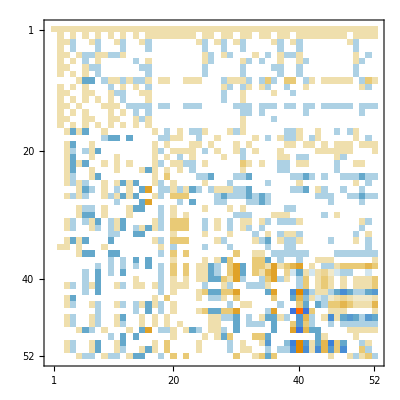
{-Graphics-,MatrixPlot[{1,2,3,12,5,13,18,37,9,14,19,38,23,40,44,52,7,11,30,20,31,33,51,24,28,34,25,32,29,36,21,45,22,8,4,10,39,41,16,43,47,15,6,46,42,50,49,35,17,27,48,26}],MatrixPlot[0]}

```mathematica
Map[MatrixPlot,(Map[Table[Coefficient[#[[2]],k],{k,Sort[vars,CompareSymbols]}]&,sols]//Inverse)//LUDecomposition]
```

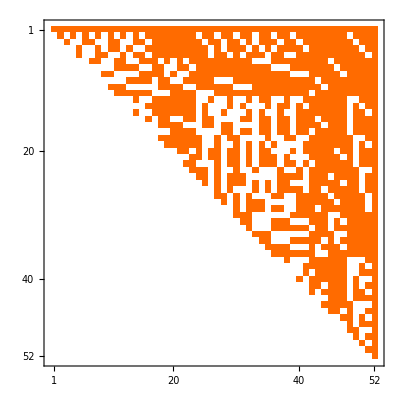

```mathematica
(Map[Table[Coefficient[#[[2]],k],{k,Sort[vars,CompareSymbols]}]&,sols]//Inverse//UpperTriangularize)//MatrixPlot
```

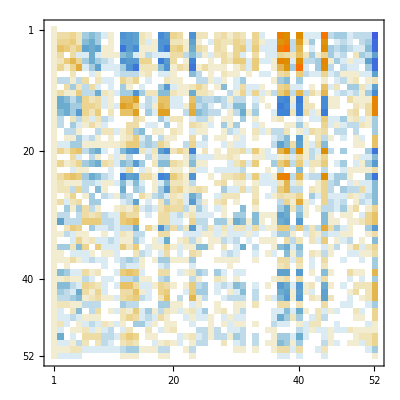

```mathematica
(Map[Table[Coefficient[#[[2]],k],{k,Sort[vars,CompareSymbols]}]&,sols]//Inverse).ConversionMatrix["C","F"]//Inverse//MatrixPlot
```

```mathematica
Simplify[(allGraphs5[lambdaKey,"colofour"]/.sols)]/.graphRep
```

--Graphics-19683--Graphics-6561--Graphics-2187--Graphics-729+-Graphics-243+-Graphics-81+-Graphics-27+2 -Graphics-26244+2 -Graphics-21870+2 -Graphics-20412--Graphics-19692--Graphics-19686+2 -Graphics-8748+2 -Graphics-7290--Graphics-6562+2 -Graphics-2916--Graphics-2430--Graphics-972--Graphics-810--Graphics-324--Graphics-270+-Graphics-244--Graphics-108-3 -Graphics-28431-3 -Graphics-26973+-Graphics-26245-3 -Graphics-22599+-Graphics-20421+-Graphics-19695-3 -Graphics-9477+-Graphics-3159+-Graphics-1053+-Graphics-351+4 -Graphics-29160

```mathematica
Simplify[(allGraphs5[alfa1Key,"colofour"]/.sols)]/.graphRep
```

--Graphics-19683--Graphics-2187--Graphics-729+-Graphics-81+-Graphics-27+-Graphics-26244+-Graphics-21870+2 -Graphics-20412+-Graphics-8748+-Graphics-7290--Graphics-6642--Graphics-6588+2 -Graphics-2916--Graphics-810--Graphics-108--Graphics-28431-2 -Graphics-26973-2 -Graphics-22599-2 -Graphics-9477+-Graphics-7371+-Graphics-6669+2 -Graphics-29160

```mathematica
Simplify[(allGraphs5[alfaKey,"colofour"]/.sols)]/.graphRep
```

--Graphics-21870--Graphics-20412+-Graphics-19684+-Graphics-28431+-Graphics-26973--Graphics-26245+2 -Graphics-22599-2 -Graphics-29160

```mathematica
Simplify[(allGraphs5[K5Key,"colofour"]/.sols)]/.graphRep
```

-6 -Graphics-19683-6 -Graphics-6561-6 -Graphics-2187-6 -Graphics-729+6 -Graphics-243+6 -Graphics-81+6 -Graphics-27+12 -Graphics-26244+12 -Graphics-21870+12 -Graphics-20412-3 -Graphics-19692-3 -Graphics-19686--Graphics-19684+12 -Graphics-8748+12 -Graphics-7290-3 -Graphics-6642-3 -Graphics-6588--Graphics-6562+12 -Graphics-2916-3 -Graphics-2430-3 -Graphics-2214--Graphics-2190-3 -Graphics-972-3 -Graphics-810--Graphics-738-6 -Graphics-324-6 -Graphics-270+-Graphics-244-6 -Graphics-108+-Graphics-84+-Graphics-36-18 -Graphics-28431-18 -Graphics-26973+2 -Graphics-26245-18 -Graphics-22599+2 -Graphics-21873+2 -Graphics-20421+2 -Graphics-19695-18 -Graphics-9477+2 -Graphics-8775+2 -Graphics-7371+2 -Graphics-6669+2 -Graphics-3159+2 -Graphics-2457+2 -Graphics-1053+6 -Graphics-351+24 -Graphics-29160

```mathematica
l=Monitor[Table[Length[ListofVars[Simplify[(allGraphs5[k,"colofour"]/.sols)]]],{k,Keys[allGraphs5]}],k]
```

{1,1,1,1,1,4,12,34,38,43,47,35,34,44,32,34,25,38,44,32,38,32,29,33,29,13,38,44,39,11,29,35,43,35,11,29,33,29,25,31,12,35,38,44,29,43,13,39,11,35,11,31,12,34,38,32,35,12,35,16,16,4,11,29,33,29,25,31,10,25,22,11,31,10,16,16,4,12,35,42,43,29,38,35,38,13,11,11,31,12,34,37,31,34,16,34,16,12,4,11,31,10,16,16,4,16,34,37,34,16,31,12,34,12,4,16,16,4,12,13,11,11,12,4,11,10,4,12,4,4,4,2,8,24,26,22,22,24,8,22,20,8,24,8,8,8,4,12,17,20,40,46,41,18,31,35,43,35,13,21,42,22,11,14,20,42,20,11,14,31,18,7,19,34,42,41,12,39,35,12,17,35,20,7,35,12,4,11,14,31,18,10,12,6,31,12,4,7,19,40,41,34,35,38,12,12,19,34,17,12,34,7,4,6,31,12,3,12,34,37,34,12,31,12,34,12,4,7,12,7,4,6,3,12,3,2,2,8,24,26,22,22,24,8,22,20,8,24,8,8,8,4,16,16,8,14,24,14,8,12,6,24,6,1,4,7,17,35,40,46,31,43,20,41,18,35,14,31,12,34,42,39,19,41,35,12,20,21,42,14,42,13,22,11,20,11,18,7,17,35,35,12,20,12,4,6,14,31,12,31,11,18,10,12,3,7,35,40,41,38,19,34,12,6,31,12,34,37,31,34,12,34,12,12,4,12,19,34,34,12,17,7,4,12,3,7,12,6,12,4,7,4,3,2,8,14,24,14,8,12,6,24,6,4,7,7,19,38,42,32,37,19,37,25,25,12,19,37,20,11,37,18,7,11,19,37,37,12,20,18,7,7,25,25,18,7,18,4,8,4,6,6,22,22,16,6,16,4,8,3,3,19,38,39,29,34,19,34,10,10,12,19,34,17,9,34,7,3,9,19,34,34,12,17,7,3,3,10,10,7,3,7,1,2,2,2,2,8,24,26,22,22,24,8,22,20,8,24,8,8,8,4,16,16,8,14,24,14,8,12,6,24,6,4,4,16,16,8,12,2,6,14,24,12,24,8,14,8,6,4,12,6,6,20,20,14,6,14,2,4,1,1,3,7,17,35,42,45,31,40,35,40,20,18,14,31,12,38,41,34,35,40,19,6,14,31,12,31,7,35,38,41,40,12,34,19,6,31,12,34,37,31,34,12,34,12,12,4,12,20,41,42,16,23,20,23,13,11,11,18,7,34,35,19,12,21,12,4,11,18,10,12,4,12,34,35,21,7,19,12,4,12,3,12,13,8,9,3,9,4,4,2,6,14,24,12,24,8,14,8,6,3,7,7,19,36,41,31,38,25,36,25,19,12,19,36,19,18,36,11,6,6,22,22,16,3,19,34,39,29,38,10,34,10,19,12,17,34,19,7,34,9,4,7,11,36,37,21,18,21,12,7,17,25,24,9,4,19,8,7,4,6,16,4,8,3,9,34,35,21,7,19,12,3,7,11,10,5,1,9,2,3,2,2,6,14,24,12,24,8,14,8,6,4,12,6,6,20,20,14,6,14,2,4,1,3,3,7,25,36,41,36,25,31,19,38,19,6,22,22,10,34,39,34,10,29,19,38,19,7,18,19,36,36,12,19,11,6,16,7,17,34,34,12,19,9,3,7,18,36,37,21,11,21,12,6,16,7,34,35,19,9,21,12,4,4,17,25,19,8,24,7,9,7,4,4,8,1,7,11,9,2,10,3,5,3,2,6,6,20,20,14,6,14,2,4,3,3,3,12,30,33,27,27,30,12,27,24,12,30,12,12,12,10,17,30,17,10,14,9,30,9,3,9,17,30,14,30,10,17,10,9,7,7,24,24,17,7,17,3,6,3,3,9,30,31,16,19,9,19,10,10,7,17,25,24,9,3,19,6,7,3,3,17,25,19,6,24,7,9,7,1,1,4,4,2,3,2,2,4,1,3,2,1,2,2,2,2,2,8,24,26,22,22,24,8,22,20,8,24,8,8,8,4,16,16,8,14,24,14,8,12,6,24,6,4,4,16,16,8,12,2,6,14,24,12,24,8,14,8,6,4,12,6,6,20,20,14,6,14,2,4,4,4,4,16,16,8,12,8,8,16,4,12,8,4,8,2,2,6,24,26,16,18,6,18,8,8,4,12,6,14,22,20,10,2,18,4,6,4,4,12,8,4,8,2,2,14,22,18,4,20,6,10,6,4,4,8,2,2,8,8,4,6,4,4,8,2,6,4,2,4,1,1,1,3,12,34,37,43,46,34,34,43,31,34,18,37,43,31,37,31,13,38,43,38,8,22,34,42,34,12,34,38,43,22,42,13,38,8,34,9,27,30,24,27,9,27,12,12,3,12,34,42,43,22,38,34,38,13,8,9,27,30,24,27,12,27,12,9,3,12,27,30,27,12,24,9,27,9,4,12,13,11,11,12,4,11,10,4,12,4,4,4,2,6,24,26,16,18,6,18,8,8,3,12,17,18,38,43,38,16,26,34,42,34,29,31,24,13,21,41,21,8,10,19,41,19,7,17,29,39,38,11,38,34,10,26,9,13,27,15,5,27,9,3,7,17,38,39,29,34,38,11,10,26,9,15,27,13,9,27,5,1,4,25,28,25,4,22,9,27,9,2,8,8,4,7,12,7,4,6,3,12,3,2,2,6,24,26,16,18,6,18,8,8,4,12,6,14,22,20,10,2,18,4,6,1,3,7,17,34,38,43,26,42,18,38,16,34,11,29,39,38,17,38,34,10,29,31,24,26,12,19,21,41,10,41,13,21,8,19,5,13,27,27,9,15,9,1,7,34,38,39,38,17,29,11,9,25,28,22,27,4,25,4,9,2,10,26,8,8,3,9,15,27,27,9,13,5,3,7,12,6,12,4,7,4,3,2,6,14,22,20,10,2,18,4,6,3,7,7,17,33,36,30,33,17,33,24,24,14,28,11,15,33,19,9,33,17,10,14,28,24,14,7,9,15,33,33,11,19,17,10,14,5,5,18,18,13,5,13,3,6,1,1,17,33,34,22,29,17,29,4,4,2,26,9,13,25,13,3,25,3,2,2,26,4,6,1,3,13,25,25,9,13,3,2,6,3,3,10,10,7,3,7,1,2,2,2,2,6,24,26,16,18,6,18,8,8,4,12,6,14,22,20,10,2,18,4,6,4,4,12,8,4,8,2,2,14,22,18,4,20,6,10,6,4,4,8,2,2,8,8,4,6,4,4,8,2,6,4,2,4,1,1,1,7,17,34,42,43,26,38,34,38,18,16,11,38,39,29,34,38,17,7,34,38,39,38,11,29,17,9,27,28,22,25,9,25,4,4,2,10,29,31,24,26,10,26,8,8,3,12,19,41,42,12,23,19,23,13,8,5,27,28,15,9,17,9,3,9,27,28,17,5,15,9,3,12,13,8,9,3,9,4,4,2,2,14,22,18,4,20,6,10,6,1,7,7,17,33,36,30,33,24,33,24,17,14,28,11,19,33,15,17,33,9,1,17,29,34,22,33,4,29,4,17,2,26,9,13,25,13,3,25,3,2,10,14,28,24,14,2,26,4,6,3,7,9,33,34,17,17,21,11,10,14,5,13,19,18,7,3,15,6,5,1,3,25,26,15,3,15,9,2,6,3,7,11,10,5,1,9,2,3,2,2,2,14,22,18,4,20,6,10,6,4,4,8,2,2,8,8,4,6,4,4,8,2,6,4,2,4,1,1,1,7,24,33,36,33,24,30,17,33,17,4,29,34,29,4,22,17,33,17,2,14,28,26,7,17,19,33,33,11,15,9,3,13,25,25,9,13,3,2,2,14,28,26,4,24,10,14,6,1,7,17,33,34,21,9,17,11,3,25,26,15,3,15,9,2,10,14,6,3,3,13,19,15,6,18,5,7,5,1,7,11,9,2,10,3,5,3,2,2,2,8,8,4,6,4,4,8,2,6,4,2,4,1,1,1,4,12,13,11,11,12,4,11,10,4,12,4,4,4,2,8,8,4,7,12,7,4,6,3,12,3,2,2,8,8,4,6,1,3,7,12,6,12,4,7,4,3,2,6,3,3,10,10,7,3,7,1,2,2,2,2,8,8,4,6,4,4,8,2,6,4,2,4,1,1,3,12,13,8,9,3,9,4,4,2,6,3,7,11,10,5,1,9,2,3,2,2,6,4,2,4,1,1,7,11,9,2,10,3,5,3,2,2,4,1,1,4,4,2,3,2,2,4,1,3,2,1,2}

```mathematica
Mean[l]//N
```

15.5873

```mathematica
l2=Monitor[Table[Length[ListofVars[Simplify[(allGraphs5[k,"colofour"]/.sols)]]],{k,Select[Keys[allGraphs5],VertexCount[allGraphs5[#,"graph"]]==5&]}],k];Mean[l2]//N
```

18.4229

```mathematica
Monitor[Table[Length[ListofVars[Simplify[(allGraphs5[k,"colofour"]/.sols)]]],{k,Select[Keys[allGraphs5],VertexCount[allGraphs5[#,"graph"]]==5&]}],k]//Mean//N
```

18.4229

```mathematica
Monitor[Table[Length[ListofVars[allGraphs5[k,"colofour"]]],{k,Select[Keys[allGraphs5],VertexCount[allGraphs5[#,"graph"]]==5&]}],k]//Mean//N
```

11.7041

```mathematica
Keys[allGraphs5[0]]
```

{signature,matrix,graph,vertexsets,vertices,edges,relations,links,parents,children,comp,compwhy,colofour,colortable,colofournull,colofourrealnull,atleast,atleastwhy,embed,colofourgenerator,colotree}

```mathematica
Monitor[Table[Length[ListofVars[allGraphs5[k,"colofournull"]]],{k,Select[Keys[allGraphs5],VertexCount[allGraphs5[#,"graph"]]==5&]}],k]//Mean//N
```

32.1572

```mathematica
Monitor[Table[Length[ListofVars[allGraphs5[k,"colofourrealnull"]]],{k,Select[Keys[allGraphs5],VertexCount[allGraphs5[#,"graph"]]==5&]}],k]//Mean//N
```

20.9297

```mathematica
Monitor[Table[Length[ListofVars[allGraphs5[k,"colotree"]]],{k,Select[Keys[allGraphs5],VertexCount[allGraphs5[#,"graph"]]==5&]}],k]//Mean//N
```

15.7979

```mathematica
Monitor[Table[Length[ListofVars[allGraphs5[k,"colofourgenerator"]]],{k,Select[Keys[allGraphs5],VertexCount[allGraphs5[#,"graph"]]==5&]}],k]//Mean//N
```

7.04492

```mathematica
Monitor[Table[Length[ListofVars[allGraphs5[k,"colofourgenerator"]]],{k,Keys[allGraphs5]}],k]//Mean//N
```

9.9029

```mathematica
Map[PartitionToTreeGraphSignature,SetPartitions[5]]
```

{29160,351,19695,9477,26245,3159,22599,6669,28431,1053,20421,8775,26973,2457,21873,7371,12,244,108,324,36,270,84,19684,6562,2916,19692,8748,738,19686,7290,2190,26244,2430,972,21870,6642,810,20412,6588,2214,1,9,3,243,81,27,19683,6561,2187,729,0}

```mathematica
Monitor[Table[Length[ListofVars[allGraphs5[k,"colofourgenerator"]]],{k,Map[PartitionToTreeGraphSignature,SetPartitions[5]]}],k]//Mean//N
```

14.4615

```mathematica
Monitor[Table[Length[ListofVars[allGraphs5[k,"colofourrealnull"]]],{k,Map[PartitionToTreeGraphSignature,SetPartitions[5]]}],k]//Mean//N
```

4.94231

```mathematica
Monitor[Table[Length[ListofVars[allGraphs5[k,"colofournull"]]],{k,Map[PartitionToTreeGraphSignature,SetPartitions[5]]}],k]//Mean//N
```

4.36538

```mathematica
Monitor[Table[Length[ListofVars[allGraphs5[k,"colofourrealnull"]]],{k,Bases["C","AtomKeys"]}],k]//Mean//N
```

6.88462

```mathematica
Monitor[Table[Length[ListofVars[allGraphs5[k,"colofour"]]],{k,Bases["E","AtomKeys"]}],k]//Mean//N
```

6.88462

```mathematica
Monitor[Table[Length[ListofVars[allGraphs5[k,"colofournull"]]],{k,Bases["G","AtomKeys"]}],k]//Mean//N
```

37.3462

```mathematica
Monitor[Table[Length[ListofVars[allGraphs5[k,"colofourgenerator"]]],{k,Bases["F","AtomKeys"]}],k]//Mean//N
```

16.5769